```mathematica
Clear["Global`*"]
```

```mathematica
Dynamic[BarChart[{i/Length@Polys,OP/NM,1},BarOrigin->Left]]
Dynamic[ListLinePlot[Flatten@δe/2]]
Dynamic[Show[G4]]
Dynamic[Show[G3NO]]
Dynamic[Show[G3VD]]
```

```mathematica
Ung=200*10^9;
ν=0.3;
DD={{λ+2*μ,λ,0},{λ,λ+2μ,0},{0,0,μ}};
λ=ν*Ung/(1+ν)/(1-2*ν);
μ=Ung/2/(1+ν);
ρ=7850;
MatrixForm@DD;
ϵ0={{α*dt},{α*dt},{0}};
α=13*10^-15;
dt=10;
ROpt=1;
a=0.5;
a1=2;
a2=3;
Reg1=Parallelogram[{3*a,2*a},{{0,a1*a},{3*a,0}}];
Reg2=Parallelogram[{3*a,2*a},{{0,a1*a},{-3*a,0}}];
Reg3=Parallelogram[{3*a,2*a},{{0,-a1*a},{3*a,0}}];
Reg4=Parallelogram[{3*a,2*a},{{0,-a1*a},{-3*a,0}}];
(*Reg5=Disk[{3a,2a},a/2];*)
Reg1234=RegionUnion[Reg1,Reg2,Reg3,Reg4];
(*ℛ=RegionDifference[Reg1234,Reg5];*)
Reg=DiscretizeRegion[Reg1234,MeshCellLabel->{0->"Index"},MaxCellMeasure->.01]
Coord=MeshCoordinates[Reg];
Polys=MeshCells[Reg,2];
```

-Graphics-

```mathematica
TimeObject[Now]
Emin=2*10^5;
E0=Ung;
DP=3;
ñ=0.2;
m=ROpt*10^(-4);
RhoMin=ROpt*10^(-1);
SquareS=Table[S[i],{i,1,Length@Polys}];
Rmin=Sqrt[Max@SquareS/Pi]*4;
Width=Table[rho[i],{i,1,Length[Polys]}];
S[i_]:=0.5*((Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]])-(Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,3]],2]]));
ai[i_]:=Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,2]],2]];
bi[i_]:=Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]];
ci[i_]:=Coord[[Polys[[i,1,3]],1]]-Coord[[Polys[[i,1,2]],1]];
(*j*)
aj[i_]:=Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,3]],2]];
bj[i_]:=Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,1]],2]];
cj[i_]:=Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]];
(*m*)
am[i_]:=Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,1]],2]];
bm[i_]:=Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,2]],2]];
cm[i_]:=Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,1]],1]];
(*Функции формы*)
Ni[i_]:=1/(2S[i])*(ai[i]+bi[i]*x+ci[i]*y);
Nj[i_]:=1/(2S[i])*(aj[i]+bj[i]*x+cj[i]*y);
Nm[i_]:=1/(2S[i])*(am[i]+bm[i]*x+cm[i]*y);
ϝ[b_]:={{DS[[NUM[b][[1]]]]},{DS[[NUM[b][[2]]]]},{DS[[NUM[b][[3]]]]},{DS[[NUM[b][[4]]]]},{DS[[NUM[b][[5]]]]},{DS[[NUM[b][[6]]]]}};
PreIntB[i_]:=Transpose[B[[i]]].DD.B[[i]];
NUM[i_]:={Polys[[i,1,1]]*2-1,Polys[[i,1,1]]*2,Polys[[i,1,2]]*2-1,Polys[[i,1,2]]*2,Polys[[i,1,3]]*2-1,Polys[[i,1,3]]*2};
Ke[i_]:=PreIntB[i]*S[i]*Width[[i]];
XC[i_]:=(Coord[[Polys[[i,1,1]],1]]+Coord[[Polys[[i,1,2]],1]]+Coord[[Polys[[i,1,3]],1]])/3;
YC[i_]:=(Coord[[Polys[[i,1,1]],2]]+Coord[[Polys[[i,1,2]],2]]+Coord[[Polys[[i,1,3]],2]])/3;
EE[i_]:=Emin+(rho[i]/ROpt)^DP*(E0-Emin);
ϝ[b_]:={{DS[[NUM[b][[1]]]]},{DS[[NUM[b][[2]]]]},{DS[[NUM[b][[3]]]]},{DS[[NUM[b][[4]]]]},{DS[[NUM[b][[5]]]]},{DS[[NUM[b][[6]]]]}};
BB[i_]:=DP*rho[i]^(DP-1)*Transpose[ϝ[i]].LocalKE[[i]].ϝ[i];
B=ParallelTable[{
{D[Ni[i],x],0,D[Nj[i],x],0,D[Nm[i],x],0},
{0,D[Ni[i],y],0,D[D[Nj[i],y]],0,D[D[Nm[i],y]]},
{D[Ni[i],y],D[Ni[i],x],D[Nj[i],y],D[Nj[i],x],D[Nm[i],y],D[Nm[i],x]}
},{i,1,Length@Polys}];
ℋ=ParallelTable[If[Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2]>0,Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2],0],{i,1,Length@Polys},{j,1,Length@Polys}];
TimeObject[Now]
```

19:44:40GMT-7.TimeObject[{19,44,40.0194},TimeZone→-7.]

19:44:47GMT-7.TimeObject[{19,44,47.7069},TimeZone→-7.]

```mathematica
λegrange=10;
NM=10;
NumberOfCycles=5;
For[i=1,i≤Length[Polys],i++,rho[i]=1];
δe=Table[0,{i,1,NumberOfCycles},{j,1,NM}];
EnergyCriteria=Table[0,{i,1,NumberOfCycles},{j,1,NM}];
For[Cycle=1,Cycle≤NumberOfCycles,Cycle++,
For[OP=1,OP≤NM,OP++,
Width=Table[rho[i],{i,1,Length[Polys]}];
LocalKE=Table[Ke[i],{i,1,Length[Polys]}];
StifnessMatrix=Table[0,{i,1,Length[Coord]*2},{j,1,Length[Coord]*2}];
For[b=1,b≤Length[Polys],b++,
For[p=1,p<=6,p++,
For[g=1,g<=6,g++,
StifnessMatrix[[NUM[b][[p]],NUM[b][[g]]]]=LocalKE[[b,p,g]]+StifnessMatrix[[NUM[b][[p]],NUM[b][[g]]]];
];
];
];
(*==========================================================================*)
(*Формирование силовых факторов и перемещений*)
Displacement=Table[δ[i],{i,1,Length[Coord]*2}];
Force=Table[f[i],{i,1,Length[Coord]*2}];
(*==========================================================================*)
(*Сосредоточенная нагрузка*)
k1=52;
k2=53;
For[i=1,i≤Length[Coord]*2,i++,
f[i]=0;
];
f[k1*2]=-100000*9.8;
f[k2*2]=-100000*9.8*0;
(*==========================================================================*)
(*Распределенные нагрузки*)
(*==========================================================================*)
(*N1=70;
N2=69;
Q=-500000*0;
L=2;
Incr=0;
For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],Incr=Incr+1]
];
FPress=Q*Abs[(Coord[[N1,1]]-Coord[[N2,1]])]*Width[[1]];*)
(*==========================================================================*)
(*For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],f[2*b-1]=f[2*b-1]+FPress/Incr]
];*)
(*==========================================================================*)
(*Формирование СЛАУ*)
J=1;(*Номер компоненты*)
H=6*a;(*Величина компоненты на границе*)
Equation={};
(*==========================================================================*)
For[i=1,i≤Length[Coord],i++,
If[Coord[[i,J]]≠H(*&&Coord[[i,J]]≠0,*),
Equation=Append[Equation,StifnessMatrix[[2i-1]].Displacement==f[2i-1]];
Equation=Append[Equation,StifnessMatrix[[2i]].Displacement==f[2i]];
];
];
(*==========================================================================*)
For[i=1,i≤Length[Coord],i++,
If[Coord[[i,J]]==H,
δ[2*i-1]=0;
δ[2*i]=0
];
(*If[Coord[[i,J]]==0,
δ[2*i-1]=0;
δ[2*i]=0
];*)
];
(*==========================================================================*)
DisplacementI={};
(*==========================================================================*)
For[i=1,i≤Length[Coord]*2,i++,
If[δ[i]≠0,DisplacementI=Append[DisplacementI,δ[i]]];
];
(*==========================================================================*)
Sols=NSolve[Equation,DisplacementI];
DS=Displacement/.Sols[[1]];
CoordDeformed={};
CoordUndeformed={};
(*==========================================================================*)
For[i=1,i≤Length[Coord],i++,
CoordDeformed=Append[CoordDeformed,{Coord[[i,1]]+DS[[2i-1]],Coord[[i,2]]+DS[[2i]]}];
CoordUndeformed=Append[CoordUndeformed,{Coord[[i,1]],Coord[[i,2]]}];
];
δe[[Cycle,OP]]=DS[[2*k1]];
EnergyCriteria[[Cycle,OP]]=Sum[Transpose[ϝ[i]].Ke[i].ϝ[i],{i,1,Length[Polys]}];
(*==========================================================================*)
(*Обратный ход для получения напряжений*)
For[b=1,b≤Length[Polys],b++,
ϵe[b]=B[b].ϝ[b];
σ[b]=DD.ϵe[b];
];
(*==========================================================================*)
(*Оптимизация формы*)
(*==========================================================================*)
DecreaseB=Table[BB[i][[1]],{i,1,Length[Polys]}]/λegrange(*Max[Table[BB[i][[1]],{i,1,Length[Polys]}]]*(3*OP)^(1/3)*);(*==========================================================================*)
For[i=1,i≤Length[Polys],i++,
If[Max[rho[i]-m,RhoMin]>rho[i]*DecreaseB[[i,1]]^ñ,
rho[i]=Max[rho[i]-m,RhoMin]
];
If[Min[rho[i]+m,ROpt]<rho[i]*DecreaseB[[i,1]]^ñ,
rho[i]=Min[rho[i]+m,ROpt],
rho[i]=rho[i]*DecreaseB[[i,1]]^ñ
];
];
(*==========================================================================*)
(*Выравнивание массы всех элементов*)
For[i=1,i<=Length[Polys],i++,If[rho[i]<RhoMin,rho[i]=RhoMin]];
For[i=1,i<=Length[Polys],i++,If[rho[i]>2,rho[i]=2]];
V1=Sum[rho[i]*S[i],{i,1,Length[Polys]}];
V2=Sum[S[i]*ROpt,{i,1,Length[Polys]}];
For[i=1,i≤Length[Polys],i++,rho[i]=rho[i]*V2/V1];
WD=Table[rho[i],{i,1,Length[Polys]}];
(*==========================================================================*)
Graph2D={};
For[v=1,v≤Length@Polys,v++,
If[WD[[v]]>0.5,
Graph2D=Append[Graph2D,
{EdgeForm[Black],Gray,Opacity[WD[[v]]],
Polygon[{
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]]},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]]},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]]}
}]}]
];
];
Graph4[OP,Cycle]=G4=Graphics[Graph2D];
(*==========================================================================*)
Graph3DNotOpt={};
For[v=1,v≤Length@Polys,v++,
If[rho[v]>0.5,
Graph3DNotOpt=Append[Graph3DNotOpt,
{EdgeForm[Thickness[0]],GrayLevel[WD[[v]]],Opacity[WD[[v]]],
Prism[{
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],rho[v]^0.5/2/2},
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],-rho[v]^0.5/2/2}
}]}]
];
];
G3NO=
Graphics3D[Graph3DNotOpt];
(*==========================================================================*)
Beep[];
];
Beep[];
(*==========================================================================*)
(*Вектор H, удаление проблемы шахматной доски.*)
ℛ=ParallelTable[(1/Sum[ℋ[[i,j]],{j,1,Length[Polys]}])*Sum[ℋ[[i,j]]*rho[j]*DP*rho[j]^(DP-1)*Transpose[ϝ[j]].LocalKE[[j]].ϝ[j],{j,1,Length[Polys]}],{i,1,Length@Polys}];FilterMatrix=ParallelTable[ℛ[[i,1,1]],{i,1,Length[Polys]}];
Beep[];
(*==========================================================================*)
V1R=Sum[FilterMatrix[[i]]*S[i],{i,1,Length[Polys]}];
FilterMatrixDensity=FilterMatrix*V2/V1R;
For[i=1,i≤Length@Polys,i++,
rho[i]=FilterMatrixDensity[[i]]
];
Graph3DOpt={};
For[v=1,v≤Length@Polys,v++,
If[rho[v]>0.5,
Graph3DOpt=Append[Graph3DOpt,
{EdgeForm[Thickness[0]],GrayLevel[rho[v]],Opacity[rho[v]],
Prism[{
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],rho[v]^0.5/2/2},
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],-rho[v]^0.5/2/2}
}]}]
];
];
G3VD=
Graphics3D[Graph3DOpt];
];
```

$Aborted

# Результаты оптимизаций различных структур

```mathematica
(*Полученные результаты*)
-Graphics3D-
-Graphics3D-
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*Export["E:\\TopologyOpt\\Gif12.avi",Animate[Show[Graph4[1,i]],{i,1,NumberOfCycles,1}]]*)
```

```mathematica
(*Animate[Show[Graph4[1,i]],{i,1,NumberOfCycles,1}]*)
```

```mathematica
(*Export["E:\\TopologyOpt\\Gif51.avi",Animate[Show[Graph33D[NM+1,i]],{i,1,NumberOfCycles,1}]]*)
```

```mathematica
(*Animate[Show[Graph3[1,i]],{i,1,NumberOfCycles,1}]*)
```

```mathematica
(*Export["E:\\TopologyOpt\\GraphDisplacement1.avi",Animate[ListLinePlot[δe[[i]],PlotLegends->{ToString[i]<>" Iteration"},PlotRange->{{1,10},{Min[δe],Max[δe]}}],{i,1,NumberOfCycles,1}]]*)
```

```mathematica
(*Animate[ListLinePlot[δe[[i]],PlotLegends->{ToString[i]<>" Iteration"},PlotRange->{{1,10},{Min[δe],Max[δe]}}],{i,1,NumberOfCycles,1}]*)
```

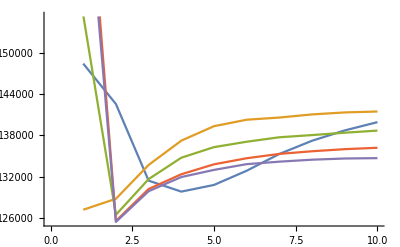

```mathematica
ListLinePlot[{Flatten@EnergyCriteria[[1]],Flatten@EnergyCriteria[[2]],Flatten@EnergyCriteria[[3]],Flatten@EnergyCriteria[[4]],Flatten@EnergyCriteria[[5]]}]
```

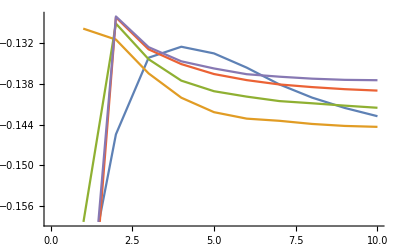

```mathematica
ListLinePlot[{Flatten@δe[[1]],Flatten@δe[[2]],Flatten@δe[[3]],Flatten@δe[[4]],Flatten@δe[[5]]}]
```

```mathematica
δe
```

{{0.170436,0.145446,0.133838,0.13183,0.132251,0.133779,0.135149,0.135782,0.13633,0.136772},{0.129229,0.121599,0.133605,0.134694,0.135733,0.135888,0.135533,0.135768,0.135702,0.135709},{0.154157,0.11455,0.131139,0.130244,0.130768,0.131026,0.131431,0.131649,0.131743,0.131847},{0.156418,0.11364,0.129673,0.128425,0.129263,0.129765,0.130299,0.130676,0.13097,0.131181},{0.150898,0.113237,0.12895,0.127643,0.128421,0.12889,0.129126,0.129451,0.129593,0.129748}}

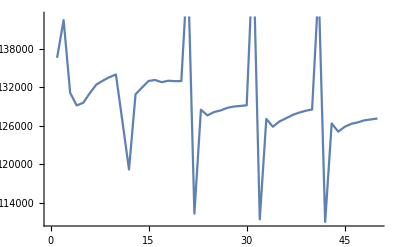

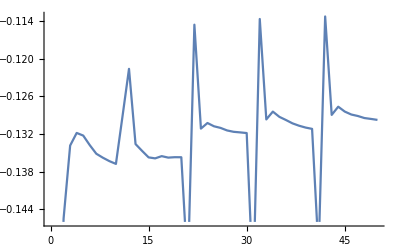

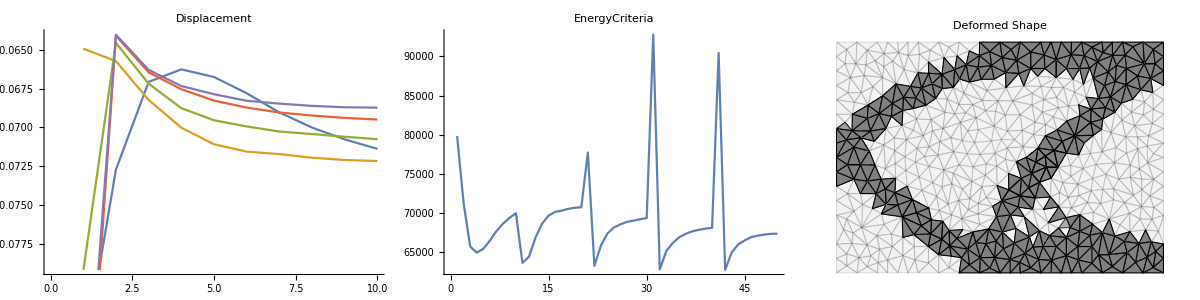

```mathematica
K1=Grid[{{
ListLinePlot[δe/2,ImageSize->Medium,PlotLabel->"Displacement"],
ListLinePlot[Flatten@EnergyCriteria/2,PlotRange->All,ImageSize->Medium,PlotLabel->"EnergyCriteria"],Show[G4,ImageSize->Medium,PlotLabel->"Deformed Shape"]}},Frame->True]
```

```mathematica
Export["E:\\TopologyOpt\\Displacement.txt",Flatten@δe/2]
Export["E:\\TopologyOpt\\DisplacementI.png",K1]
```

E:\TopologyOpt\Displacement.txt

E:\TopologyOpt\DisplacementI.png